# POLARIZATION OF CHARGED SPHERICAL DIELECTRIC CORE-SHELL

A. Marin, O. Ianc, T. O. Cheche

University of Bucharest, Faculty of Physics, Măgurele, PO BOX MG11, 077125, Romania

Two point charges are placed in a spherical dielectric  core-shell embedded in a dielectric environment, one of the charges being located in the core and the other in the shell. The core, shell, and environment are characterized by different dielectric constants. Analytical solutions for the electrostatic energy of the system and the polarization charge density at the core-shell and shell-environment interfaces are obtained by a classical approach.

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True]
```

# 1) Potential generated by q1 located in core (ρ, diel ct ϵ1). W11: q1, q2 in core. -Graphics-

```mathematica
(* Charge q1 in the inside sphere of radius ρ and diel ct ϵ1 *)
FullSimplify[Solve[{q1*(ct/ϵ1)*s1^n/ρ^(n+1)+a*ρ^n==b*ρ^n+c/ρ^(n+1),
-(n+1)*q1*ct*s1^n/ρ^(n+2)+n*ϵ1*a*ρ^(n-1)==n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c/ρ^(n+2),
b*R^n+c/R^(n+1)==d/R^(n+1),
n*ϵ2*b*R^(n-1)-(n+1)*ϵ2*c/R^(n+2)==-(n+1)*ϵ2*d/R^(n+2)},{a,b,c,d}],Assumptions:>{ρ>0,R>0,s1>0,s2>0}]
ct->(4 Subscript[πϵ, 0])^-1
```

{{a→(0.5^n (-0.00795775-0.00795775 n) ρ^(-1.-2. n))/(0.6+1. n),b→0.,c→(0.5^n (0.0159155+0.031831 n))/(0.6+1. n),d→(0.5^n (0.0159155+0.031831 n))/(0.6+1. n)}}

1/(4 π)→1/(4 πϵ_0)

```mathematica
{{a->(ct (1+n) q1 ((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n) ρ^(1+2 n)) s1^n)/(ϵ1 (ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(2+4 n)+ϵ1 (ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R ρ (R ρ)^(2 n)),b->(ct (ϵ2-ϵ3) (1+n) (1+2 n) q1 s1^n)/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n)),c->(ct (1+2 n) (ϵ3+(ϵ2+ϵ3) n) q1 R^(1+2 n) s1^n)/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n)),d->(ct ϵ2 (1+2 n)^2 q1 R^(1+2 n) s1^n)/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n))}}
```

{{a→(0.5^n (1+n) (-2.^(1+2 n) (4+7 n)-(2+5 n) ρ^(1+2 n)))/(4 π (4. 2.^(2 n) (3+5 n) (4+7 n) ρ^(1+2 n)+2 n (1+n) ρ^(2+4 n))),b→-(0.5^n (1+n) (1+2 n))/(4 π (2.^(1+2 n) (3+5 n) (4+7 n)+n (1+n) ρ^(1+2 n))),c→(0.5^n 2.^(1+2 n) (1+2 n) (4+7 n))/(4 π (2.^(1+2 n) (3+5 n) (4+7 n)+n (1+n) ρ^(1+2 n))),d→(3 0.5^n 2.^(1+2 n) (1+2 n)^2)/(4 π (2.^(1+2 n) (3+5 n) (4+7 n)+n (1+n) ρ^(1+2 n)))}}

```mathematica
A1[n_]:=(ct  q1 s1^n)/R^(1+2 n)PereA1equiv[n]; B1[n_]:=(ct q1 s1^n)/R^(1+2 n)PereB1equiv[n]; 
C1[n_]:=ct q1  s1^n PereC1equiv[n]; D1[n_]:=ct q1  s1^n PereD1equiv[n];
PereA1equiv[n_]:=(1/(ϵ1* Dn[n])(1+n)((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)/ρ^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (ϵ2-ϵ3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (ϵ3+(ϵ2+ϵ3) n))/Dn[n])^1;
PereD1equiv[n_]:=((ϵ2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n)/R^(1+2 n);
```

```mathematica
Polarization energy
```

energy Polarization

```mathematica
W11=ct*(-1/(eps1*(se-sh))+PereA1equiv[n]/R^(2*n+1)*((se^(2n)+sh^(2n))/2-se^n sh^n*Pn));

W11/.ϵ2->ϵ1
```

(-1/(eps1 (se-sh))+(2.^(-1-2 n) (1+n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))) (-2-5 n-2.^(1+2 n) (4+7 n) ρ^(-1-2 n)))/(2 ((2+5 n) (4+7 n)+2.^(-1-2 n) n (1+n) ρ^(1+2 n))))/(4 π)

```mathematica
ct (-1/(eps1 (se-sh))+((ϵ1-ϵ3) (1+n) R^(-1-2 n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))))/(ϵ1 (ϵ3+(ϵ1+ϵ3) n)))
```

(-1/(eps1 (se-sh))-(2.^(-1-2 n) (1+n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))))/(4+6 n))/(4 π)

# 2) Check for 1)

## 2.1 Potential for core ρ=R; Brus problem -Graphics-

```mathematica
Print["Dn(n)= ",Dn[n]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 2]];
Print["A1[n]= ",Simplify[A1[n]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 2]]];
Print["B1[n]= ",Simplify[B1[n]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 2]]];
Print["C1[n]= ",Simplify[C1[n]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 2]]];
Print["D1[n]= ",Simplify[D1[n]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 2]]];
```

Dn(n)= 2.^(-1-2 n) n (1+n) ρ^(1+n ϵ_1)+(5 n+ϵ_2) (7 n+ϵ_2)

A1[n]= (0.0625 0.5^n ⅇ^(-1.38629 n) (1+n) (-2-5 n-2. 2.^(n ϵ_1) ρ^(-1-2 n) (7 n+ϵ_2)))/(1.5708 ⅇ^(-1.38629 n) n (1+n) ρ^(1+n ϵ_1)+π (5 n+ϵ_2) (7 n+ϵ_2))

B1[n]= -(0.125 0.5^n ⅇ^(-1.38629 n) (1+n) (1+n ϵ_1))/(1.5708 ⅇ^(-1.38629 n) n (1+n) ρ^(1+n ϵ_1)+π (5 n+ϵ_2) (7 n+ϵ_2))

C1[n]= (0.5^n (1+n ϵ_1) (7 n+ϵ_2))/(4 (1.5708 ⅇ^(-1.38629 n) n (1+n) ρ^(1+n ϵ_1)+π (5 n+ϵ_2) (7 n+ϵ_2)))

D1[n]= (3 0.5^n (1+n ϵ_1)^ϵ_1)/(4 (1.5708 ⅇ^(-1.38629 n) n (1+n) ρ^(1+n ϵ_1)+π (5 n+ϵ_2) (7 n+ϵ_2)))

## 2.2 Check1: ϵ3=1; ϵ2=1 (*Same! as Bottcher p. 83 *)

```mathematica
ϵ3=1;ϵ2=1; 
FullSimplify[Solve[{q1*(ct/ϵ1)*s1^n/ρ^(n+1)+a*ρ^n==0*q2*(ct/ϵ2)*ρ^n/s2^(n+1)+b*ρ^n+c/ρ^(n+1),
-(n+1)*q1*ct*s1^n/ρ^(n+2)+n*ϵ1*a*ρ^(n-1)==0*n*q2*ct*ρ^(n-1)/s2^(n+1)+n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c/ρ^(n+2),
0*q2*(ct/ϵ2)*s2^n/R^(n+1)+b*R^n+c/R^(n+1)==d/R^(n+1),
-(n+1)*0*q2*ct*s2^n/R^(n+2)+n*ϵ2*b*R^(n-1)-(n+1)*ϵ2*c/R^(n+2)==-(n+1)*ϵ3*d/R^(n+2)},{a,b,c,d}]]/.ϵ1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1
```

{{a→((0.0132629+0.0132629 n) r_0^(-1.-2. n) s_1^n)/(0.333333+1. n),b→0.,c→((0.0265258+0.0530516 n) s_1^n)/(0.333333+1. n),d→((0.0265258+0.0530516 n) s_1^n)/(0.333333+1. n)}}

```mathematica
ϵ3=1;ϵ2=1;
Print["A[",n,"]= ",FullSimplify[A1[n]]/.ϵ1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["B[",n,"]= ",FullSimplify[B1[n]]/.ϵ1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["C[",n,"]= ",FullSimplify[C1[n]]/.ϵ1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["D[",n,"]= ",FullSimplify[D1[n]]/.ϵ1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Clear[n,q1,ϵ1,ϵ2,ϵ3];
```

A[n]= (0.0397887 (1+n) r_0^(-1-2 n) s_1^n)/(1+3 n)

B[n]= 0

C[n]= (s_1^n (1+n ϵ_1))/(4 (π+3 n π))

D[n]= (s_1^n (1+n ϵ_1))/(4 (π+3 n π))

## 2.3 Check2: ϵ3=ϵ2=ϵ3

```mathematica
ϵ1=ϵ2=ϵ3;
Print["A[",n,"]= ",FullSimplify[A1[n]]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["B[",n,"]= ",FullSimplify[B1[n]]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["C[",n,"]= ",FullSimplify[C1[n]]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["D[",n,"]= ",FullSimplify[D1[n]]/.ϵ1->Subscript[ϵ, 1]/.ϵ2->Subscript[ϵ, 2]/.ϵ3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ρ->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];Clear[n,q1,ϵ1,ϵ2,ϵ3];
```

A[n]= 0

B[n]= 0

C[n]= (q1 s_1^n)/(4 ϵ_1 πϵ_0)

D[n]= (q1 s_1^n)/(4 ϵ_1 πϵ_0)

# 3) Charge q2 in layer (ρ, R and diel. ct. ϵ2). W12, W22 -Graphics-

## 3.1 Potential generated by q2 located in layer of radius ρ <->R and diel ct ϵ2

```mathematica
Clear[a,b,c,d];FullSimplify[Solve[{a*ρ^n==q2*(ct/ϵ2)*ρ^n/s2^(n+1)+b*ρ^n+c/ρ^(n+1),
n*ϵ1*a*ρ^(n-1)==n*q2*ct*ρ^(n-1)/s2^(n+1)+n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c/ρ^(n+2),
q2*(ct/ϵ2)*s2^n/R^(n+1)+b*R^n+c/R^(n+1)==d/R^(n+1),
-(n+1)*q2*ct*s2^n/R^(n+2)+n*ϵ2*b*R^(n-1)-(n+1)*ϵ2*c/R^(n+2)==-(n+1)*ϵ3*d/R^(n+2)},{a,b,c,d}]]
```

{{a→(ⅇ^(-0.405465 n) (ⅇ^(0.81093 n) (ϵ2 (n^2 (0.0795775+(0.238732+0.159155 n) n) ϵ1^2+n (0.159155+n (0.63662+(0.795775+0.31831 n) n)) ϵ1 ϵ2+(0.0795775+n (0.397887+n (0.716197+(0.557042+0.159155 n) n))) ϵ2^2)+(n^2 (-0.0795775+(-0.238732-0.159155 n) n) ϵ1^2+n (-0.159155+n (-0.63662+(-0.795775-0.31831 n) n)) ϵ1 ϵ2+(-0.0795775+n (-0.397887+n (-0.716197+(-0.557042-0.159155 n) n))) ϵ2^2) ϵ3)+ⅇ^(1.38629 n) (n ϵ2 ((0.106103+0.212207 n) n^2 ϵ1^2+n (0.212207+(0.63662+0.424413 n) n) ϵ1 ϵ2+(0.106103+n (0.424413+(0.530516+0.212207 n) n)) ϵ2^2)+(n^2 (0.106103+(0.31831+0.212207 n) n) ϵ1^2+n (0.212207+n (0.848826+(1.06103+0.424413 n) n)) ϵ1 ϵ2+(0.106103+n (0.530516+n (0.95493+(0.742723+0.212207 n) n))) ϵ2^2) ϵ3)) ρ^1.)/((1. n ϵ1+1. ϵ2+1. n ϵ2)^2 (ⅇ^(1.38629 n) (2. ϵ2 ϵ3+n^2 (2. ϵ1 ϵ2+2. ϵ2^2+2. ϵ1 ϵ3+2. ϵ2 ϵ3)+n (2. ϵ2^2+2. ϵ1 ϵ3+4. ϵ2 ϵ3)) ρ^1.+n ((1.+1. n) ϵ1 ϵ2+(-1.-1. n) ϵ2^2+(-1.-1. n) ϵ1 ϵ3+(1.+1. n) ϵ2 ϵ3) ρ^(2.+2 n))),b→-((1. (1/ρ^2. ⅇ^(-0.980829 n) (ϵ2 (0.00994718 ϵ2-0.00994718 ϵ3)+n (0.00994718 ϵ1 ϵ2+0.0198944 ϵ2^2-0.00994718 ϵ1 ϵ3-0.0198944 ϵ2 ϵ3)+n^2 (0.00994718 ϵ1 ϵ2+0.00994718 ϵ2^2-0.00994718 ϵ1 ϵ3-0.00994718 ϵ2 ϵ3))+ⅇ^(-1.79176 n) n ((-0.00663146-0.00663146 n) ϵ1 ϵ2+(0.00663146+0.00663146 n) ϵ2^2+(0.00663146+0.00663146 n) ϵ1 ϵ3+(-0.00663146-0.00663146 n) ϵ2 ϵ3) ρ^(-1.+2. n)))/(ϵ2 (-(0.25 (1. ϵ2+n (1. ϵ1+ϵ2)) (1. n ϵ2+1. ϵ3+1. n ϵ3))/ρ^2.-0.125 ⅇ^(-1.38629 n) n (1. ϵ1-1. ϵ2) ((1.+1. n) ϵ2+(-1.-1. n) ϵ3) ρ^(-1.+2 n)))),c→(ⅇ^(-0.405465 n) n (ⅇ^(1.38629 n) (n ϵ2 (0.106103 n ϵ1^2+0.106103 ϵ1 ϵ2-0.106103 ϵ2^2-0.106103 n ϵ2^2)+((0.106103+0.106103 n) n ϵ1^2+(0.106103+0.106103 n) ϵ1 ϵ2-0.106103 (1.+1. n)^2 ϵ2^2) ϵ3)+ⅇ^(0.81093 n) (n^2 (ϵ1^2 (0.0795775 ϵ2-0.0795775 ϵ3)+ϵ2^2 (-0.0795775 ϵ2+0.0795775 ϵ3))+n (ϵ1^2 (0.0795775 ϵ2-0.0795775 ϵ3)+ϵ1 ϵ2 (0.0795775 ϵ2-0.0795775 ϵ3)+ϵ2^2 (-0.159155 ϵ2+0.159155 ϵ3))+ϵ2 (0.0795775 ϵ1 ϵ2-0.0795775 ϵ2^2-0.0795775 ϵ1 ϵ3+0.0795775 ϵ2 ϵ3))) ρ^(2.+2. n))/(ϵ2 (1. n ϵ1+1. ϵ2+1. n ϵ2) (ⅇ^(1.38629 n) (-2. ϵ2 ϵ3+n (-2. ϵ2^2-2. ϵ1 ϵ3-4. ϵ2 ϵ3)+n^2 (-2. ϵ1 ϵ2-2. ϵ2^2-2. ϵ1 ϵ3-2. ϵ2 ϵ3)) ρ^1.+n (ϵ2 (1. ϵ2+1. n ϵ2-1. ϵ3-1. n ϵ3)+ϵ1 (-1. ϵ2-1. n ϵ2+1. ϵ3+1. n ϵ3)) ρ^(2.+2 n))),d→(ⅇ^(-0.405465 n) (ⅇ^(2.19722 n) ((0.0795775+0.159155 n) n^2 ϵ1^2+n (0.159155+(0.477465+0.31831 n) n) ϵ1 ϵ2+(0.0795775+n (0.31831+(0.397887+0.159155 n) n)) ϵ2^2) ρ^1.+ⅇ^(1.38629 n) n ((-0.0530516 ϵ1+0.0530516 ϵ2) ϵ2+n^2 (-0.106103 ϵ1^2+0.106103 ϵ2^2)+n (-0.0530516 ϵ1^2-0.106103 ϵ1 ϵ2+0.159155 ϵ2^2)) ρ^(2.+2. n)))/((1. n ϵ1+1. ϵ2+1. n ϵ2) (ⅇ^(1.38629 n) (1. ϵ2 ϵ3+n^2 (1. ϵ1 ϵ2+1. ϵ2^2+1. ϵ1 ϵ3+1. ϵ2 ϵ3)+n (1. ϵ2^2+1. ϵ1 ϵ3+2. ϵ2 ϵ3)) ρ^1.+n ((0.5+0.5 n) ϵ1 ϵ2+(-0.5-0.5 n) ϵ2^2+(-0.5-0.5 n) ϵ1 ϵ3+(0.5+0.5 n) ϵ2 ϵ3) ρ^(2.+2 n)))}}

```mathematica
{{a->(ct (1+2 n) q2 s2^(-1-n) ((ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ2-ϵ3) (1+n) s2^(1+2 n)))/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n)),b->(ct (ϵ2-ϵ3) (1+n) q2 s2^(-1-n) ((-ϵ1+ϵ2) n ρ^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)))/(ϵ2 ((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n))),c->-(ct (ϵ1-ϵ2) q2 ρ^(1+2 n) s2^(-1-n) (n (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ2-ϵ3) n (1+n) s2^(1+2 n)))/(ϵ2 ((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n))),d->(ct (1+2 n) q2 R^(1+2 n) s2^(-1-n) (-((ϵ1-ϵ2) n ρ^(1+2 n))+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)))/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n))}}
```

{{a→(1.5^(-1-n) (1+2 n) (1.5^(1+2 n) (1+n) (ϵ2-ϵ3)+2.^(1+2 n) (ϵ3+n (ϵ2+ϵ3))))/(4 π (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (1+n) (ϵ1-ϵ2) (ϵ2-ϵ3) ρ^(1+2 n))),b→(1.5^(-1-n) (1+n) (ϵ2-ϵ3) (1.5^(1+2 n) (ϵ2+n (ϵ1+ϵ2))+n (-ϵ1+ϵ2) ρ^(1+2 n)))/(4 π ϵ2 (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (1+n) (ϵ1-ϵ2) (ϵ2-ϵ3) ρ^(1+2 n))),c→-(1.5^(-1-n) (ϵ1-ϵ2) (1.5^(1+2 n) n (1+n) (ϵ2-ϵ3)+2.^(1+2 n) n (ϵ3+n (ϵ2+ϵ3))) ρ^(1+2 n))/(4 π ϵ2 (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (1+n) (ϵ1-ϵ2) (ϵ2-ϵ3) ρ^(1+2 n))),d→(1.5^(-1-n) 2.^(1+2 n) (1+2 n) (1.5^(1+2 n) (ϵ2+n (ϵ1+ϵ2))-n (ϵ1-ϵ2) ρ^(1+2 n)))/(4 π (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (1+n) (ϵ1-ϵ2) (ϵ2-ϵ3) ρ^(1+2 n)))}}

```mathematica
A2[n_]:=ct* PereA2equiv[n,s2]*q2  s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2  s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2  ρ^(1+2 n) s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  ρ^(1+2 n) s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((ϵ3+(ϵ2+ϵ3) n) +(ϵ2-ϵ3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ2-ϵ3) (1+n)  ((-ϵ1+ϵ2) n ρ^(1+2 n)/R^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ1-ϵ2)   (-n (ϵ3+(ϵ2+ϵ3) n) +(-ϵ2+ϵ3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(ϵ1-ϵ2) n +(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/ρ^(1+2 n)))/Dn[n])^1;

Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) ρ^(1+2 n)/R^(1+2 n);
```

## 3.2 Polarization energy check: W11=W22=W12 if ϵ1=ϵ2.

```mathematica
AA1=Simplify[(PereB2equiv[n,se]+PereC2equiv[n,se])1/(2*se)];
AA2=Simplify[(PereB2equiv[n,sh]+PereC2equiv[n,sh])1/(2*sh)];
BB2=Pn*Simplify[(PereB2equiv[n,se]+PereC2equiv[n,sh])*sh^n/se^(n+1)+((PereB2equiv[n,sh]+PereC2equiv[n,se])se^n/sh^(n+1))]/2;
W22=ct*(-1/(eps2 (se-sh))+Simplify[(AA1+AA2-BB2)]);

Simplify[W22/.ϵ2->ϵ1]

W11/.ϵ2->ϵ1
Simplify[(W22-W11)/.ϵ2->ϵ1/.eps2->eps1]
```

-1/(4 eps2 π se-4 eps2 π sh)+(0.0198944 ⅇ^(-1.38629 n) (1+n) se^(2 n) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3)))-(0.0397887 ⅇ^(-1.38629 n) (1+n) Pn se^n sh^n (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3)))+(0.0198944 ⅇ^(-1.38629 n) (1+n) sh^(2 n) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3)))

(-1/(eps1 (se-sh))+(2.^(-1-2 n) (1+n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))) (-2-5 n-2.^(1+2 n) (4+7 n) ρ^(-1-2 n)))/(2 ((3+5 n) (4+7 n)+2.^(-1-2 n) n (1+n) ρ^(1+2 n))))/(4 π)

ⅇ^(-1.38629 n) (1/(ϵ1 (ϵ3+n (ϵ1+ϵ3)))(se^(2 n) ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3)+sh^(2 n) ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3)+Pn se^n sh^n ((-0.0397887-0.0397887 n) ϵ1+(0.0397887+0.0397887 n) ϵ3))-(0.00994718 (1+n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)) (-2-5 n-2. ⅇ^(1.38629 n) (4+7 n) ρ^(-1-2 n)))/((3+5 n) (4+7 n)+0.5 ⅇ^(-1.38629 n) n (1+n) ρ^(1+2 n)))

```mathematica
ct (-1/(eps2 se-eps2 sh)+((ϵ1-ϵ3) (1+n) R^(-1-2 n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)))/(2 ϵ1 (ϵ3+ϵ1 n+ϵ3 n)))
```

(-1/(eps2 se-eps2 sh)+(2.^(-1-2 n) (1+n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)) (ϵ1-ϵ3))/(2 ϵ1 (n ϵ1+ϵ3+n ϵ3)))/(4 π)

```mathematica
ct (-1/(eps1 (se-sh))+((ϵ1-ϵ3) (1+n) R^(-1-2 n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))))/(ϵ1 (ϵ3+(ϵ1+ϵ3) n)))
```

(-1/(eps1 (se-sh))+(2.^(-1-2 n) (1+n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3))))/(4 π)

```mathematica
n=0;
Simplify[W22/.ϵ2->ϵ1,Assumptions:>{ρ>0}]
Clear[ρ,n]
Limit[W22/.ϵ2->ϵ1,ρ->0,Assumptions:>n>=0]
Limit[W22/.ϵ2->ϵ3,ρ->0,Assumptions:>n>=0]
n=0;Limit[W22/.ϵ2->ϵ1,ρ->0]
Clear[ρ,n]
```

(0.-1/(eps2 se-eps2 sh)+((0.5-0.5 Pn) ϵ1)/(0.+ϵ1 ϵ3)+((-0.5+0.5 Pn) ϵ3)/(0.+ϵ1 ϵ3))/(4 π)

1/(4 π)(-1/(eps2 (se-sh))+(-Pn (ⅇ^(-1.38629 n) (1+n) se^(-1-n) sh^n (0.+0.5 se^(1+2 n) (ϵ1+2 n ϵ1)) (ϵ1-ϵ3)+ⅇ^(-1.38629 n) (1+n) se^n sh^(-1-n) (0.+0.5 sh^(1+2 n) (ϵ1+2 n ϵ1)) (ϵ1-ϵ3))+(ⅇ^(-1.38629 n) (1+n) (0.+0.5 se^(1+2 n) (ϵ1+2 n ϵ1)) (ϵ1-ϵ3))/se+(ⅇ^(-1.38629 n) (1+n) (0.+0.5 sh^(1+2 n) (ϵ1+2 n ϵ1)) (ϵ1-ϵ3))/sh)/(2 ϵ1 (0.+(ϵ1+2 n ϵ1) (ϵ3+n (ϵ1+ϵ3)))))

1/(4 π)(-1/(eps2 (se-sh))+(((ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3)))/se+((ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3)))/sh-Pn (se^n sh^(-1-n) (ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3))+se^(-1-n) sh^n (ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3))))/(2 ϵ3 (0.+(ϵ3+2 n ϵ3) (ϵ3+n (ϵ1+ϵ3)))))

1/(4 π)(-1/(eps2 (se-sh))+(-Pn ((0.+1. (0.+0.5 se ϵ1) (ϵ1-ϵ3))/se+(0.+1. (0.+0.5 sh ϵ1) (ϵ1-ϵ3))/sh)+(0.+1. (0.+0.5 se ϵ1) (ϵ1-ϵ3))/se+(0.+1. (0.+0.5 sh ϵ1) (ϵ1-ϵ3))/sh)/(2 ϵ1 (0.+ϵ1 ϵ3)))

```mathematica
ct (-((ϵ1-ϵ3) (-1+Pn))/(ϵ1 ϵ3 R)-1/(eps2 se-eps2 sh))
```

(-1/(eps2 se-eps2 sh)-(0.5 (-1+Pn) (ϵ1-ϵ3))/(ϵ1 ϵ3))/(4 π)

```mathematica
ct (-1/(eps2 se-eps2 sh)+((ϵ1-ϵ3) (1+n) R^(-1-2 n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)))/(2 ϵ1 (ϵ3+ϵ1 n+ϵ3 n)))
```

(-1/(eps2 se-eps2 sh)+(2.^(-1-2 n) (1+n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)) (ϵ1-ϵ3))/(2 ϵ1 (n ϵ1+ϵ3+n ϵ3)))/(4 π)

```mathematica
ct (-1/(eps2 se-eps2 sh)+((ϵ1-ϵ3) n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))))/(2 ϵ3 (ϵ3+ϵ1 n+ϵ3 n)))
```

(-1/(eps2 se-eps2 sh)+(n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))) (ϵ1-ϵ3))/(2 ϵ3 (n ϵ1+ϵ3+n ϵ3)))/(4 π)

```mathematica
-((ct (ϵ1 (ϵ3 R+eps2 (-1+Pn) (se-sh))-ϵ3 eps2 (-1+Pn) (se-sh)))/(ϵ1 ϵ3 eps2 R (se-sh)))
```

-(0.0397887 (-eps2 (-1+Pn) (se-sh) ϵ3+ϵ1 (eps2 (-1+Pn) (se-sh)+2. ϵ3)))/(eps2 (se-sh) ϵ1 ϵ3)

```mathematica
Limit[W22/.ϵ2->ϵ3,ρ->0,Assumptions:>n>=0]
```

1/(4 π)(-1/(eps2 (se-sh))+(((ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3)))/se+((ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3)))/sh-Pn (se^n sh^(-1-n) (ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3))+se^(-1-n) sh^n (ϵ1-ϵ3) (0.-n (ϵ3+2 n ϵ3))))/(2 ϵ3 (0.+(ϵ3+2 n ϵ3) (ϵ3+n (ϵ1+ϵ3)))))

```mathematica
ct (-1/(eps2 se-eps2 sh)+((ϵ1-ϵ3) n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))))/(2 ϵ3 (ϵ3+ϵ1 n+ϵ3 n)))
```

(-1/(eps2 se-eps2 sh)+(n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))) (ϵ1-ϵ3))/(2 ϵ3 (n ϵ1+ϵ3+n ϵ3)))/(4 π)

```mathematica
W12=ct/2*(PereA1equiv[n] sh^(2*n)/R^(2*n+1)+PereB2equiv[n,se] 1/se+PereC2equiv[n,se] ρ^(2*n+1)/se^(2n+2)-Pn*((PereA2equiv[n,se]+PereC1equiv[n])sh^n/se^(n+1)+PereB1equiv[n]*R^(-2*n-1)sh^n se^n));
W12ϵ2ϵ1p=FullSimplify[W12/.ϵ2->ϵ1]
Simplify[(W11-W12)/.ϵ2->ϵ1/.eps2->eps1];
```

1/(ϵ1 (ϵ3+n (ϵ1+ϵ3)))ⅇ^(-1.38629 n) se^(-1-n) (se^(1+3 n) ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3)+se^(1+n) sh^(2 n) ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3)+sh^n (Pn se^(1+2 n) ((-0.0397887-0.0397887 n) ϵ1+(0.0397887+0.0397887 n) ϵ3)+ⅇ^(1.38629 n) Pn (-0.0795775 n ϵ1-0.0795775 ϵ3-0.0795775 n ϵ3)))

```mathematica
1/(2 ϵ1 (ϵ3+(ϵ1+ϵ3) n))ct R^(-1-2 n) se^(-1-n) ((ϵ1-ϵ3) (1+n) se^(1+3 n)-2 Pn ((ϵ3+(ϵ1+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ3) (1+n) se^(1+2 n)) sh^n+(ϵ1-ϵ3) (1+n) se^(1+n) sh^(2 n))
```

1/(8 π ϵ1 (ϵ3+n (ϵ1+ϵ3)))2.^(-1-2 n) se^(-1-n) ((1+n) se^(1+3 n) (ϵ1-ϵ3)+(1+n) se^(1+n) sh^(2 n) (ϵ1-ϵ3)-2 Pn sh^n ((1+n) se^(1+2 n) (ϵ1-ϵ3)+2.^(1+2 n) (ϵ3+n (ϵ1+ϵ3))))

```mathematica
W12ϵ2ϵ1p=1/(2 ϵ1 (ϵ3+(ϵ1+ϵ3) n))ct R^(-1-2 n) se^(-1-n) ((ϵ1-ϵ3) (1+n) se^(1+3 n)-2 Pn ((ϵ3+(ϵ1+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ3) (1+n) se^(1+2 n)) sh^n+(ϵ1-ϵ3) (1+n) se^(1+n) sh^(2 n));

v3=1/(2 ϵ1 (ϵ3+ϵ1 n+ϵ3 n))ct   (R^(-1-2 n)(se^(2 n)+sh^(2 n))(1+n)(-ϵ3+ϵ1)+ 2 Pn  (-sh^n se^(-1-n)(ϵ3(1+n)+n *ϵ1)-R^(-1-2 n)(1+n)(ϵ1-ϵ3)se^n sh^n));
W12ϵ2ϵ1=1/(2 ϵ1 (ϵ3+ϵ1 n+ϵ3 n))ct   (R^(-1-2 n)(se^(2 n)+sh^(2 n))(1+n)(-ϵ3+ϵ1)- 2 Pn  R^(-1-2 n)(1+n)(ϵ1-ϵ3)se^n sh^n)+-Pn/ϵ1 ct sh^n se^(-1-n)  ;
Simplify[W12ϵ2ϵ1p-W12ϵ2ϵ1]
```

0.

# 4) Check for 3) -Graphics-

## 4.1 Check1: ϵ3=1; ϵ2=1 (*Same! as Bottcher p. 86 *)

```mathematica
Print["A2[n]= ",Simplify[A2[n]/.ϵ2->1/.ϵ3->1, Assumptions->n>=0]];
Print["B2[n]= ",Simplify[B2[n]/.ϵ2->1/.ϵ3->1, Assumptions->n>=0]];
Print["C2[n]= ",Simplify[C2[n]/.ϵ2->1/.ϵ3->1, Assumptions->n>=0]];
Print["D2[n]= ",FullSimplify[D2[n]/.ϵ2->1/.ϵ3->1, Assumptions->n>=0]];
```

A2[n]= (ⅇ^(-0.405465 n) (0.0530516+0.106103 n))/(1.+n+n ϵ1)

B2[n]= 0

C2[n]= -(0.0530516 ⅇ^(-0.405465 n) n (-1.+ϵ1) ρ^(1+2 n))/(1.+n+n ϵ1)

D2[n]= (ⅇ^(-0.405465 n) (ⅇ^(0.81093 n) (0.0795775+n (0.0795775+0.0795775 ϵ1))+n (0.0530516-0.0530516 ϵ1) ρ^(1+2 n)))/(1.+n+n ϵ1)

## 4.2 Check2: ϵ3=ϵ2=ϵ3

```mathematica
ϵ1=ϵ2=ϵ3;
Print["A2[n]= ",Simplify[A2[n], Assumptions->n>=0]];
Print["B2[n]= ",Simplify[B2[n], Assumptions->n>=0]];
Print["C2[n]= ",Simplify[C2[n], Assumptions->n>=0]];
Print["D2[n]= ",FullSimplify[D2[n], Assumptions->n>=0]];
Clear[ϵ1,ϵ2,ϵ3]
```

A2[n]= (0.0530516 ⅇ^(-0.405465 n))/ϵ3

B2[n]= 0

C2[n]= 0

D2[n]= 1.5^n/(4 π ϵ3)

# 5) Charge q out in environment with diel. ct. ϵ3. W13 -Graphics-

## 5.1 Potential generated by q3 located in solvent.

```mathematica
V3=FullSimplify[Solve[{a*ρ^n==b*ρ^n+c*ρ^(-n-1),n*ϵ1*a*ρ^(n-1)==n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c*ρ^(-n-2),b*R^n+c*R^(-n-1)==(ct/ϵ3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*ϵ2*b*R^(n-1)-(n-1)*ϵ2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*ϵ3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ρ>0,R>0}]
```

{{a→(0.31831 ⅇ^(1.38629 n) (0.5+1. n) q3 s3^(-1.-1. n) ϵ2 (n (0.5+1. n) ϵ1+0.5 ϵ2+n (1.5+1. n) ϵ2) ρ^1.)/((1. n ϵ1+1. ϵ2+1. n ϵ2) (ⅇ^(1.38629 n) (1. ϵ2 ϵ3+n^2 (1. ϵ1 ϵ2+1. ϵ2^2+1. ϵ1 ϵ3+1. ϵ2 ϵ3)+n (1. ϵ2^2+1. ϵ1 ϵ3+2. ϵ2 ϵ3)) ρ^1.+n ((-0.5+0.5 n) ϵ1 ϵ2+(0.5-0.5 n) ϵ2^2+(-0.5-0.5 n) ϵ1 ϵ3+(0.5+0.5 n) ϵ2 ϵ3) ρ^(2.+2 n))),b→-((1. (0.0198944+0.0397887 n) q3 s3^(-1.-1. n) (1. n ϵ1+(1.+n) ϵ2))/(ρ^2. (-(0.25 (1. ϵ2+n (1. ϵ1+ϵ2)) (1. n ϵ2+1. ϵ3+1. n ϵ3))/ρ^2.-0.125 ⅇ^(-1.38629 n) n (1. ϵ1-1. ϵ2) ((-1.+1. n) ϵ2+(-1.-1. n) ϵ3) ρ^(-1.+2 n)))),c→-((0.159155 ⅇ^(1.38629 n) n q3 s3^(-1.-1. n) (1. ϵ1-1. ϵ2) (n (0.5+1. n) ϵ1+0.5 ϵ2+n (1.5+1. n) ϵ2) ρ^(2.+2. n))/((1. n ϵ1+1. ϵ2+1. n ϵ2) (ⅇ^(1.38629 n) (1. ϵ2 ϵ3+n^2 (1. ϵ1 ϵ2+1. ϵ2^2+1. ϵ1 ϵ3+1. ϵ2 ϵ3)+n (1. ϵ2^2+1. ϵ1 ϵ3+2. ϵ2 ϵ3)) ρ^1.+n ((-0.5+0.5 n) ϵ1 ϵ2+(0.5-0.5 n) ϵ2^2+(-0.5-0.5 n) ϵ1 ϵ3+(0.5+0.5 n) ϵ2 ϵ3) ρ^(2.+2 n)))),d→(n q3 s3^(-1.-1. n) (ⅇ^(2.77259 n) (n^2 (ϵ1^2 (-0.31831 ϵ2+0.31831 ϵ3)+ϵ2^2 (-0.31831 ϵ2+0.31831 ϵ3)+ϵ1 ϵ2 (-0.63662 ϵ2+0.63662 ϵ3))+ϵ2^2 (-0.31831 ϵ2+0.31831 ϵ3)+n ϵ2 (-0.63662 ϵ1 ϵ2-0.63662 ϵ2^2+0.63662 ϵ1 ϵ3+0.63662 ϵ2 ϵ3)) ρ^1.+ⅇ^(1.38629 n) ((0.159155 ϵ1-0.159155 ϵ2) ϵ2^2+n^2 (ϵ1^2 (-0.159155 ϵ2-0.159155 ϵ3)+ϵ2^2 (0.159155 ϵ2+0.159155 ϵ3))+n ϵ2 (0.159155 ϵ1^2-0.159155 ϵ1 ϵ2-0.159155 ϵ1 ϵ3+0.159155 ϵ2 ϵ3)) ρ^(2.+2. n)))/((1. n ϵ1+1. ϵ2+1. n ϵ2) ϵ3 (ⅇ^(1.38629 n) (2. ϵ2 ϵ3+n^2 (2. ϵ1 ϵ2+2. ϵ2^2+2. ϵ1 ϵ3+2. ϵ2 ϵ3)+n (2. ϵ2^2+2. ϵ1 ϵ3+4. ϵ2 ϵ3)) ρ^1.+n ((-1.+1. n) ϵ1 ϵ2+(1.-1. n) ϵ2^2+(-1.-1. n) ϵ1 ϵ3+(1.+1. n) ϵ2 ϵ3) ρ^(2.+2 n)))}}

```mathematica
{{a->(ct ϵ2 (1+2 n)^2 q3 R^(1+2 n) s3^(-1-n))/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) n (ϵ2 (-1+n)-ϵ3 (1+n)) ρ^(1+2 n)),b->(ct (1+2 n) (ϵ2+(ϵ1+ϵ2) n) q3 R^(1+2 n) s3^(-1-n))/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) n (ϵ2 (-1+n)-ϵ3 (1+n)) ρ^(1+2 n)),c->-((ct (ϵ1-ϵ2) n (1+2 n) q3 R ρ (R ρ)^(2 n) s3^(-1-n))/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) n (ϵ2 (-1+n)-ϵ3 (1+n)) ρ^(1+2 n))),d->1/s3 ct q3 R (-((R^2/s3)^n)/ϵ3+((1+2 n) R^(2 n) ((ϵ2+(ϵ1+ϵ2) n) R^(1+2 n)+(-ϵ1+ϵ2) n ρ^(1+2 n)) s3^-n)/((ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)+(ϵ1-ϵ2) n (ϵ2 (-1+n)-ϵ3 (1+n)) ρ^(1+2 n)))}}
```

{{a→(2.^(1+2 n) (1+2 n)^2 q3 s3^(-1-n) ϵ2)/(4 π (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3) ρ^(1+2 n))),b→(2.^(1+2 n) (1+2 n) q3 s3^(-1-n) (ϵ2+n (ϵ1+ϵ2)))/(4 π (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3) ρ^(1+2 n))),c→-(0.159155 2.^(2 n) n (1+2 n) q3 s3^(-1-n) (ϵ1-ϵ2) ρ^(1+2 n))/(2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3) ρ^(1+2 n)),d→(0.159155 q3 (-(4.^n (1/s3)^n)/ϵ3+(2.^(2 n) (1+2 n) s3^-n (2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2))+n (-ϵ1+ϵ2) ρ^(1+2 n)))/(2.^(1+2 n) (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))+n (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3) ρ^(1+2 n))))/s3}}

```mathematica
Gn[n_]:=n ρ^(1+2n)/R^(1+2 n) (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3)+ (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3));
A3s[n_]:=(ct (1+2 n)^2 q3  s3^(-1-n) ϵ2)/Gn[n];(**)
A3[n_]:=(ct  q3)/s3^(1+n)PereA3equiv[n];
PereA3equiv[n_]:=((1+2 n)^2  ϵ2)/Gn[n];
```

```mathematica
B3s[n_]:=ct (1+2 n) q3  s3^(-1-n) (ϵ2+n (ϵ1+ϵ2))/Gn[n];
B3[n_]:=(ct  q3)/s3^(1+n) PereB3equiv[n];
PereB3equiv[n_]:=((1+2 n) (ϵ2+n (ϵ1+ϵ2)))/Gn[n];
```

```mathematica
C3s[n_]:=-ct n (1+2 n) q3 * s3^(-1-n) *ρ^(2 n+1) (ϵ1-ϵ2)/Gn[n];
C3[n_]:=ct  q3 ρ^(2 n+1)/s3^(1+n) PereC3equiv[n];
PereC3equiv[n_]:=(n (1+2 n) (ϵ2-ϵ1))/Gn[n];
```

```mathematica
D3[n_]:=ct  q3 R^(2 n+1)/s3^(1+n) PereD3equiv[n];
PereD3equiv[n_]:= (-1/ϵ3+((1+2 n)  (n ρ^(1+2n)/R^(2 n+1) (-ϵ1+ϵ2)+(ϵ2+n (ϵ1+ϵ2))))/Gn[n]);
```

## 5.1# Potential generated by q3 located in solvent-check

```mathematica
V3=FullSimplify[Solve[{a*ρ^n==b*ρ^n+c*ρ^(-n-1),n*ϵ1*a*ρ^(n-1)==n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c*ρ^(-n-2),b*R^n+c*R^(-n-1)==(ct/ϵ3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*ϵ2*b*R^(n-1)-(n-1)*ϵ2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*ϵ3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ρ>0,R>0}];
A3[n_]:=q3 (ct ϵ2 (1+2 n)^2 ) s3^(-1-n)/G[n];

B3[n_]:=q3 (ct (1+2 n) (ϵ2+(ϵ1+ϵ2) n) ) s3^(-1-n)/G[n];

C3[n_]:=-q3 (ct (ϵ1-ϵ2) n (1+2 n) (ρ)^(2 n+1) ) s3^(-1-n)/G[n];


D3[n_]:=ct q3* s3^(-1-n)*(-R^(1+2 n)/ϵ3+1/G[n](1+2 n) *((ϵ2+(ϵ1+ϵ2) n) R^(1+2 n)+(-ϵ1+ϵ2) n ρ^(1+2 n)) );

D3[n_]:=ct q3* s3^(-1-n)*R^(1+2 n)(-G[n]  +(1+2 n) *ϵ3*(ϵ2+(ϵ1+ϵ2) n +(-ϵ1+ϵ2) n (ρ/R)^(1+2 n)) )/(ϵ3*G[n]);
G[n_]:=n ρ^(1+2n)/R^(1+2 n) (ϵ1-ϵ2) ((-1+n) ϵ2-(1+n) ϵ3)+ (ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3));
```

## 5.2 Polarization energy check: W13(ϵ2=ϵ1)=W12(ϵ2=ϵ1)

```mathematica
W13=ct/2 Simplify[((PereA1equiv[n]*sh^(2n)/R^(2 n+1)+PereD3equiv[n]*R^(2 n+1)/se^(2n+2))-(PereD1equiv[n]+PereA3equiv[n])sh^n/se^(n+1)*Pn)];
W13ϵ2ϵ1=Simplify[W13/.ϵ2->ϵ1]
```

1/(ϵ1 ϵ3 (ϵ3+n (ϵ1+ϵ3)))ⅇ^(-1.38629 n) se^(-2 (1+n)) (ⅇ^(2.77259 n) n ϵ1 (-0.0795775 ϵ1+0.0795775 ϵ3)+ⅇ^(1.38629 n) (-0.0795775-0.159155 n) Pn se^(1+n) sh^n ϵ1 ϵ3+se^(2+2 n) sh^(2 n) ϵ3 ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3))

```mathematica
1/2 ct (((-ϵ1+ϵ3) n R^(1+2 n) se^(-2 (1+n)))/(ϵ3 (ϵ3+ϵ1 n+ϵ3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(ϵ3+ϵ1 n+ϵ3 n)+((ϵ1-ϵ3) (1+n) R^(-1-2 n) sh^(2 n))/(ϵ1 (ϵ3+(ϵ1+ϵ3) n)))
```

(-(2 (1+2 n) Pn se^(-1-n) sh^n)/(n ϵ1+ϵ3+n ϵ3)+(2.^(1+2 n) n se^(-2 (1+n)) (-ϵ1+ϵ3))/(ϵ3 (n ϵ1+ϵ3+n ϵ3))+(2.^(-1-2 n) (1+n) sh^(2 n) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3))))/(8 π)

```mathematica
W12ϵ2ϵ3=Simplify[W12/.ϵ2->ϵ3]
```

1/(ϵ1 ϵ3 (ϵ3+n (ϵ1+ϵ3)))se^(-2 (1+n)) ρ^(-1-2 n) (se^(2+2 n) sh^(2 n) ϵ3 ((0.0397887+0.0397887 n) ϵ1+(-0.0397887-0.0397887 n) ϵ3)+(-0.0795775-0.159155 n) Pn se^(1+n) sh^n ϵ1 ϵ3 ρ^(1+2 n)+n ϵ1 (-0.0397887 ϵ1+0.0397887 ϵ3) ρ^(2+4 n))

```mathematica
(ct (-((ϵ1-ϵ3) n ρ^(1+2 n) se^(-2 (1+n)))/ϵ3-2 (1+2 n) Pn se^(-1-n) sh^n+((ϵ1-ϵ3) (1+n) ρ^(-1-2 n) sh^(2 n))/ϵ1))/(2 (ϵ3+(ϵ1+ϵ3) n))
```

(-2 (1+2 n) Pn se^(-1-n) sh^n+((1+n) sh^(2 n) (ϵ1-ϵ3) ρ^(-1-2 n))/ϵ1-(n se^(-2 (1+n)) (ϵ1-ϵ3) ρ^(1+2 n))/ϵ3)/(8 π (ϵ3+n (ϵ1+ϵ3)))

```mathematica
FullSimplify[W13ϵ2ϵ1-W12ϵ2ϵ3]/.ρ->R
```

1/(ϵ1 ϵ3 (ϵ3+n (ϵ1+ϵ3)))2.^(-1-2 n) ⅇ^(-1.38629 n) se^(-2 (1+n)) (2.^(1+2 n) ⅇ^(2.77259 n) n ϵ1 (-0.0795775 ϵ1+0.0795775 ϵ3)+2.^(1+2 n) se^(2+2 n) sh^(2 n) ϵ3 ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3)+ⅇ^(1.38629 n) (2.^(2+4 n) n ϵ1 (0.0397887 ϵ1-0.0397887 ϵ3)+se^(2+2 n) sh^(2 n) ϵ3 (-0.0397887 ϵ1-0.0397887 n ϵ1+0.0397887 ϵ3+0.0397887 n ϵ3)))

```mathematica
Simplify[W12/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
Simplify[W13/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
```

-(Pn se^(-1-n) sh^n)/(4 π ϵ)

-(0.0795775 Pn se^(-1-n) sh^n)/ϵ

```mathematica
Simplify[Dn[n]-Gn[n]]
```

ⅇ^(-1.38629 n) n (1. ϵ1-1. ϵ2) ϵ2 ρ^(1+2 n)

```mathematica
2 (ϵ1-ϵ2) ϵ2 n R^(-1-2 n) ρ^(1+2 n)
```

2 2.^(-1-2 n) n (ϵ1-ϵ2) ϵ2 ρ^(1+2 n)

## 5.3 Polarization energy check: W23

```mathematica
W23=ct/2 Simplify[((PereB2equiv[n,sh]*1/sh+PereC2equiv[n,sh]*ρ^(2 n+1)/sh^(2n+2)+PereD3equiv[n] R^(2 n+1)/se^(2n+2))-((PereD2equiv[n,sh]+PereC3equiv[n])ρ^(2 n+1)/(se^(n+1)*sh^(n+1))+PereB3equiv[n] sh^n/se^(n+1))*Pn)];
W23ϵ2ϵ1=Simplify[W23/.ϵ2->ϵ1]
W13ϵ2ϵ1
Simplify[W23ϵ2ϵ1-W13ϵ2ϵ1]
```

1/(ϵ1 ϵ3 (ϵ3+n (ϵ1+ϵ3)))ⅇ^(-1.38629 n) se^(-2 (1+n)) (ⅇ^(2.77259 n) n ϵ1 (-0.0795775 ϵ1+0.0795775 ϵ3)+ⅇ^(1.38629 n) (-0.0795775-0.159155 n) Pn se^(1+n) sh^n ϵ1 ϵ3+se^(2+2 n) sh^(2 n) ϵ3 ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3))

1/(ϵ1 ϵ3 (ϵ3+n (ϵ1+ϵ3)))ⅇ^(-1.38629 n) se^(-2 (1+n)) (ⅇ^(2.77259 n) n ϵ1 (-0.0795775 ϵ1+0.0795775 ϵ3)+ⅇ^(1.38629 n) (-0.0795775-0.159155 n) Pn se^(1+n) sh^n ϵ1 ϵ3+se^(2+2 n) sh^(2 n) ϵ3 ((0.0198944+0.0198944 n) ϵ1+(-0.0198944-0.0198944 n) ϵ3))

0

```mathematica
1/2 ct (((-ϵ1+ϵ3) n R^(1+2 n) se^(-2 (1+n)))/(ϵ3 (ϵ3+ϵ1 n+ϵ3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(ϵ3+(ϵ1+ϵ3) n)+((ϵ1-ϵ3) (1+n) R^(-1-2 n) sh^(2 n))/(ϵ1 (ϵ3+(ϵ1+ϵ3) n)))
```

((2.^(1+2 n) n se^(-2 (1+n)) (-ϵ1+ϵ3))/(ϵ3 (n ϵ1+ϵ3+n ϵ3))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(ϵ3+n (ϵ1+ϵ3))+(2.^(-1-2 n) (1+n) sh^(2 n) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3))))/(8 π)

```mathematica
1/2 ct (((-ϵ1+ϵ3) n R^(1+2 n) se^(-2 (1+n)))/(ϵ3 (ϵ3+ϵ1 n+ϵ3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(ϵ3+ϵ1 n+ϵ3 n)+((ϵ1-ϵ3) (1+n) R^(-1-2 n) sh^(2 n))/(ϵ1 (ϵ3+(ϵ1+ϵ3) n)))
```

(-(2 (1+2 n) Pn se^(-1-n) sh^n)/(n ϵ1+ϵ3+n ϵ3)+(2.^(1+2 n) n se^(-2 (1+n)) (-ϵ1+ϵ3))/(ϵ3 (n ϵ1+ϵ3+n ϵ3))+(2.^(-1-2 n) (1+n) sh^(2 n) (ϵ1-ϵ3))/(ϵ1 (ϵ3+n (ϵ1+ϵ3))))/(8 π)

```mathematica
Simplify[W12/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
Simplify[W13/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
Simplify[W23/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
```

-(Pn se^(-1-n) sh^n)/(4 π ϵ)

-(0.0795775 Pn se^(-1-n) sh^n)/ϵ

-(0.0795775 Pn se^(-1-n) sh^n)/ϵ

## 5.4 Polarization energy check: W33

```mathematica
W33=ct*Simplify[-1/(eps3*(se-sh))+(PereD3equiv[n]*R^(2 n+1)(1/(2 sh^(2n+2))+1/(2 se^(2n+2))-1/(se^(n+1)*sh^(n+1))*Pn))];
Simplify[W33/.ϵ1->ϵ/.ϵ2->ϵ/.ϵ3->ϵ]
```

-0.0795775/(eps3 se-1. eps3 sh)

# 6) Check for 5)

```mathematica
(*Check 1:*) ϵ3=ϵ2=ϵ1;FullSimplify[Solve[{a*ρ^n==b*ρ^n+c*ρ^(-n-1),n*ϵ1*a*ρ^(n-1)==n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c*ρ^(-n-2),b*R^n+c*R^(-n-1)==(ct/ϵ3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*ϵ2*b*R^(n-1)-(n-1)*ϵ2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*ϵ3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ρ>0,R>0}]/.ϵ1->Subscript[ϵ, 1]/.ρ->Subscript[r, 0]
Simplify[A3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ρ->Subscript[r, 0]]
Simplify[B3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ρ->Subscript[r, 0]]
Simplify[C3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ρ->Subscript[r, 0]]
Simplify[D3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ρ->Subscript[r, 0]]

Clear[n,q1,q2,ϵ1,ϵ2,ϵ3];
```

{{a→(0.0795775 q3 s3^(-1.-1. n))/ϵ_1,b→(0.0795775 q3 s3^(-1.-1. n))/ϵ_1,c→0.,d→0.}}

(q3 s3^(-1-n))/(4 π ϵ1)

(q3 s3^(-1-n))/(4 π ϵ1)

0

0.

```mathematica
(ct q3 s3^(-1-n))/ϵ1
```

(q3 s3^(-1-n))/(4 π ϵ1)

```mathematica
(ct q3 s3^(-1-n))/ϵ1
```

(q3 s3^(-1-n))/(4 π ϵ1)

```mathematica
(*Check 2:Bottcher p. 86*)ϵ2=ϵ1=ϵ;ϵ3=1;
FullSimplify[Solve[{a*ρ^n==b*ρ^n+c*ρ^(-n-1),n*ϵ1*a*ρ^(n-1)==n*ϵ2*b*ρ^(n-1)-(n+1)*ϵ2*c*ρ^(-n-2),b*R^n+c*R^(-n-1)==(ct/ϵ3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*ϵ2*b*R^(n-1)-(n-1)*ϵ2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*ϵ3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ρ>0,R>0}]/.ct->(4 Subscript[πϵ, 0])^-1
Simplify[A3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ρ->Subscript[r, 0]]
Simplify[B3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ρ->Subscript[r, 0]]
Simplify[C3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ρ->Subscript[r, 0]]
Simplify[D3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ρ->Subscript[r, 0]]
Clear[n,q1,q2,ϵ1,ϵ2,ϵ3,ρ,R];
```

{{a→((0.0795775+0.159155 n) q3 s3^(-1.-1. n))/(1.+1. n+1. n ϵ),b→((0.0795775+0.159155 n) q3 s3^(-1.-1. n))/(1.+1. n+1. n ϵ),c→0.,d→(ⅇ^(1.38629 n) n q3 s3^(-1.-1. n) (0.0795775+n (0.159155-0.159155 ϵ)-0.0795775 ϵ))/((0.5+1. n) (1.+1. n+1. n ϵ))}}

((1+2 n) q3 s3^(-1-n))/(4 π (1+n+n ϵ))

((1+2 n) q3 s3^(-1-n))/(4 π (1+n+n ϵ))

0

-(0.159155 ⅇ^(1.38629 n) n q3 s3^(-1-n) (-1.+ϵ))/(1.+n+n ϵ)

# 7) Potentials ϕ_1, ϕ_2

## 7.1 Potentials ϕ_1, ϕ_2

7.1.1ϕ_1 generated by q_1 located in core

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,q1,Nn];

(*--------------------------*)
ϕ1[s1_,r_,t1_]:=Which[
0<r≤s1,∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*s1)(r/s1)^n+A1[n]*r^n)*P[n,t1],
s1<r≤r0,∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*P[n,t1],

r0<r<R,∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*P[n,t1],
r>R,∑_(n=0)^Nn D1[n]*r^(-n-1)*P[n,t1]];

(*Next, definition of ϕ1 as piecewise potential: {ϕ1S,ϕ1L,ϕ12,ϕ13}*)
ϕ1S[s1_,r_,t1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*s1)(r/s1)^n+A1[n]*r^n)*P[n,t1];
ϕ1L[s1_,r_,t1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*P[n,t1];
ϕ12[s1_,r_,t1_]:=∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*P[n,t1];
ϕ13[s1_,r_,t1_]:=∑_(n=0)^Nn D1[n]*r^(-n-1)*P[n,t1];
(*Next, definition of parameters*)
ct=(4*π*ϵ0)^-1;
A1[n_]:=Simplify[(ct * q1 *s1^n)/R^(1+2 n)PereA1equiv[n]]; B1[n_]:=Simplify[(ct *q1 *s1^n)/R^(1+2 n)PereB1equiv[n]]; 
C1[n_]:=Simplify[ct *q1 * s1^n PereC1equiv[n]]; D1[n_]:=Simplify[ct* q1 * s1^n PereD1equiv[n]];
PereA1equiv[n_]:=(1/(ϵ1* Dn[n])(1+n)((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)/r0^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (ϵ2-ϵ3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (ϵ3+(ϵ2+ϵ3) n))/Dn[n])^1;
PereD1equiv[n_]:=((ϵ2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
Print["***********************"]
Print["A1[n]=",A1[n]]
Print["B1[n]=",B1[n]]
Print["C1[n]=",C1[n]]
Print["D1[n]=",D1[n]]
Print["PARTICULAR CASE ϵ2=ϵ3=1"]
Print["A1[n]=",A1[n]/.ϵ2->1/.ϵ3->1]
Print["B1[n]=",B1[n]/.ϵ2->1/.ϵ3->1]
Print["C1[n]=",C1[n]/.ϵ2->1/.ϵ3->1]
Print["D1[n]=",D1[n]/.ϵ2->1/.ϵ3->1]
Print["PARTICULAR CASE ϵ1=ϵ2=ϵ3"]
Print["A1[n]=",Simplify[A1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["B1[n]=",Simplify[B1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["C1[n]=",Simplify[C1[n]//.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["D1[n]=",Simplify[D1[n]//.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
```

***********************

A1[n]=((1+n) q1 R^(-1-2 n) s1^n ((ϵ1+n (ϵ1+ϵ2)) (ϵ2-ϵ3)+R^(1+2 n) r0^(-1-2 n) (ϵ1-ϵ2) (ϵ3+n (ϵ2+ϵ3))))/(4 π ϵ0 ϵ1 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

B1[n]=((1+n) (1+2 n) q1 R^(-1-2 n) s1^n (ϵ2-ϵ3))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

C1[n]=((1+2 n) q1 s1^n (ϵ3+n (ϵ2+ϵ3)))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

D1[n]=((1+2 n)^2 q1 s1^n ϵ2)/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

PARTICULAR CASE ϵ2=ϵ3=1

A1[n]=((1+n) q1 r0^(-1-2 n) s1^n (-1+ϵ1))/(4 π ϵ0 ϵ1 (1+n (1+ϵ1)))

B1[n]=0

C1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (1+n (1+ϵ1)))

D1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (1+n (1+ϵ1)))

PARTICULAR CASE ϵ1=ϵ2=ϵ3

A1[n]=0

B1[n]=0

C1[n]=(q1 s1^n)/(4 π ϵ0 ϵ1)

D1[n]=(q1 s1^n)/(4 π ϵ0 ϵ1)

7.1.2 ϕ_2 generated by q_2 located in shell

```mathematica
Clear[r0,r, R,ϵ0,ϵ1,ϵ2,ϵ3,s2,q2,Nn,r1,r2,r3,r4];
(*--------------------------*)
ϕ2[s2_,r_,t2_]:=Which[
0<r≤r0,∑_(n=0)^Nn A2[n]*r^n*P[n,t2],
r0<r≤s2,∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2],
s2<r≤R,∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2],r>R,∑_(n=0)^Nn D2[n]*r^(-n-1)*P[n,t2]];

(*Next, definition of ϕ2 as piecewise potential: {ϕ21,ϕ2S,ϕ2L,ϕ23}*)
ϕ21[s2_,r_,t2_]:=∑_(n=0)^Nn A2[n]*r^n*P[n,t2];
ϕ2S[s2_,r_,t2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2];
ϕ2L[s2_,r_,t2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2];
ϕ23[s2_,r_,t2_]:=∑_(n=0)^Nn D2[n]*r^(-n-1)*P[n,t2];

ct=(4*π*ϵ0)^-1;
A2[n_]:=ct* PereA2equiv[n,s2]*q2 * s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2 * s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2 * r0^(1+2 n) *s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  *r0^(1+2 n) *s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((ϵ3+(ϵ2+ϵ3) n) +(ϵ2-ϵ3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ2-ϵ3) (1+n)  ((-ϵ1+ϵ2) n r0^(1+2 n)/R^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ1-ϵ2)   (-n (ϵ3+(ϵ2+ϵ3) n) +(-ϵ2+ϵ3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(ϵ1-ϵ2) n +(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/r0^(1+2 n)))/Dn[n])^1;

Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
Print["***********************"]
Print["A2[n]=",A2[n]]
Print["B2[n]=",B2[n]]
Print["C2[n]=",C2[n]]
Print["D2[n]=",D2[n]]
Print["PARTICULAR CASE ϵ2=ϵ3=1"]
Print["A2[n]=",A2[n]/.ϵ2->1/.ϵ3->1]
Print["B2[n]=",B2[n]/.ϵ2->1/.ϵ3->1]
Print["C2[n]=",C2[n]/.ϵ2->1/.ϵ3->1]
Print["D2[n]=",D2[n]/.ϵ2->1/.ϵ3->1]
Print["PARTICULAR CASE ϵ1=ϵ2=ϵ3"]
Print["A2[n]=",Simplify[A2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["B2[n]=",Simplify[B2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["C2[n]=",Simplify[C2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["D2[n]=",Simplify[D2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
```

***********************

A2[n]=((1+2 n) q2 s2^(-1-n) ((1+n) R^(-1-2 n) s2^(1+2 n) (ϵ2-ϵ3)+ϵ3+n (ϵ2+ϵ3)))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

B2[n]=((1+n) q2 s2^(-1-n) (n R^(-1-2 n) r0^(1+2 n) (-ϵ1+ϵ2)+R^(-1-2 n) s2^(1+2 n) (ϵ2+n (ϵ1+ϵ2))) (ϵ2-ϵ3))/(4 π ϵ0 ϵ2 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

C2[n]=(q2 r0^(1+2 n) s2^(-1-n) (ϵ1-ϵ2) (n (1+n) R^(-1-2 n) s2^(1+2 n) (-ϵ2+ϵ3)-n (ϵ3+n (ϵ2+ϵ3))))/(4 π ϵ0 ϵ2 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

D2[n]=((1+2 n) q2 r0^(1+2 n) s2^(-1-n) (n (-ϵ1+ϵ2)+r0^(-1-2 n) s2^(1+2 n) (ϵ2+n (ϵ1+ϵ2))))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

PARTICULAR CASE ϵ2=ϵ3=1

A2[n]=((1+2 n) q2 s2^(-1-n))/(4 π ϵ0 (1+n (1+ϵ1)))

B2[n]=0

C2[n]=-(n q2 r0^(1+2 n) s2^(-1-n) (-1+ϵ1))/(4 π ϵ0 (1+n (1+ϵ1)))

D2[n]=(q2 r0^(1+2 n) s2^(-1-n) (n (1-ϵ1)+r0^(-1-2 n) s2^(1+2 n) (1+n (1+ϵ1))))/(4 π ϵ0 (1+n (1+ϵ1)))

PARTICULAR CASE ϵ1=ϵ2=ϵ3

A2[n]=(q2 s2^(-1-n))/(4 π ϵ0 ϵ1)

B2[n]=0

C2[n]=0

D2[n]=(q2 s2^n)/(4 π ϵ0 ϵ1)

7.1.3 Graphs ϕ_1 & ϕ_2

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,s2,q1,q2,Nn];
r0=1; R=2;ϵ0=1;ϵ1=2;ϵ2=3;ϵ3=4; s1=0.5;s2=1.5;q1=q2=1;
t1=t2=π/4;Nn=4;
```

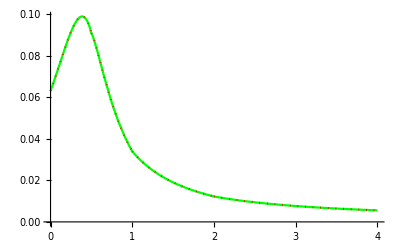

```mathematica
p1S=Plot[ϕ1S[s1,r,t1],{r,0,s1},PlotStyle->{Red,Dotted}];
p1L=Plot[ϕ1L[s1,r,t1],{r,s1,r0},PlotStyle->{Red,Dotted}];
p12=Plot[ϕ12[s1,r,t1],{r,r0,R},PlotStyle->{Red,Dotted}];
p13=Plot[ϕ13[s1,r,t1],{r,R,2*R},PlotStyle->{Red,Dotted}];
(*Plot[ϕ1[s1,r,t1],{r,r0/3,2*r0/3}](*cusp due to slow convergence of the sums*)*)
p1=Plot[ϕ1[s1,r,t1],{r,0,2*R},PlotStyle->{Green}];
Show[p1,p1S,p1L,p12,p13]
```

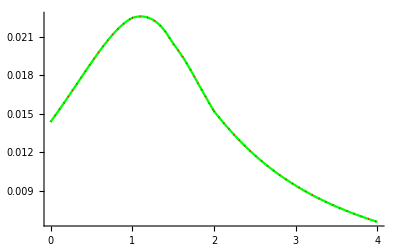

```mathematica
p21=Plot[ϕ21[s2,r,t2],{r,0,r0},PlotStyle->{Red,Dotted}];
p2S=Plot[ϕ2S[s2,r,t2],{r,r0,s2},PlotStyle->{Red,Dotted}];
p2L=Plot[ϕ2L[s2,r,t2],{r,s2,R},PlotStyle->{Red,Dotted}];
p23=Plot[ϕ23[s2,r,t2],{r,R,2*R},PlotStyle->{Red,Dotted}];
p2=Plot[ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Green}];
Show[p2,p21,p2S,p2L,p23]
```

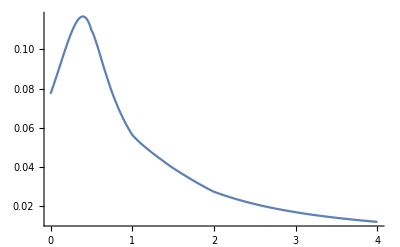

```mathematica
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0}]
```

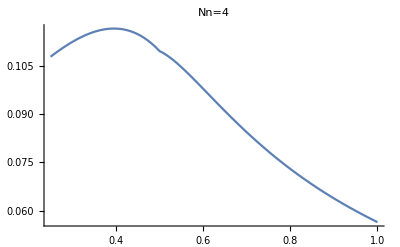

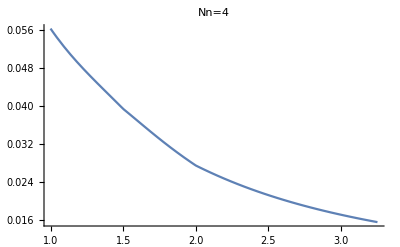

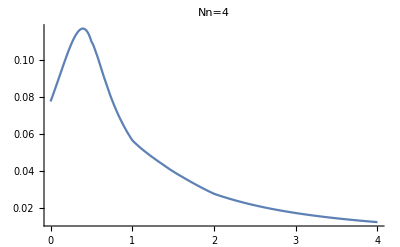

```mathematica
(*Nn=4*)
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,s1/2,r0},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,r0,r0+3*s2/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
```

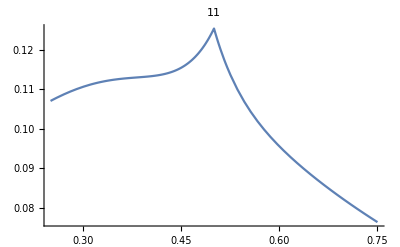

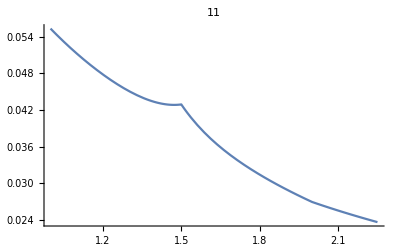

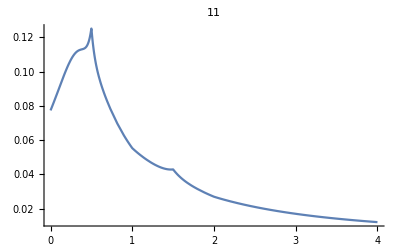

```mathematica
Nn=452;
Nn=11;
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,s1/2,3*s1/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,r0,3*s2/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn](**)
```

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,s2,q1,q2,Nn];
```

## 7.2 Check ϕ_1+ϕ_2 convergence with the parameters from 7.1

Potential for Nn=29

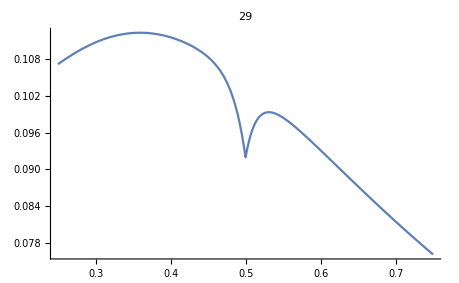
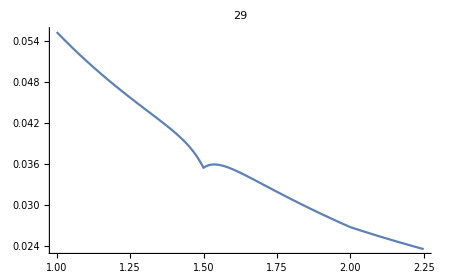
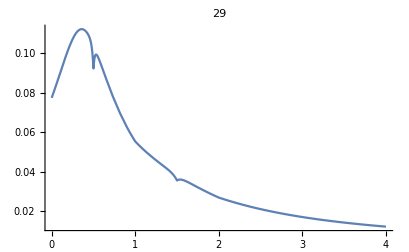

Potential for Nn=129

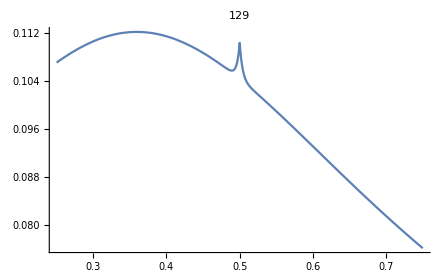
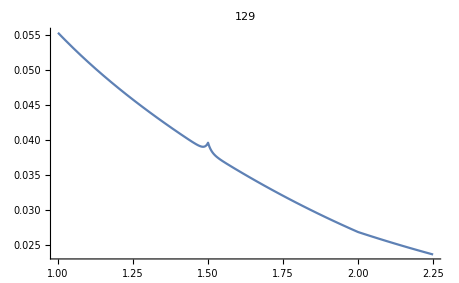
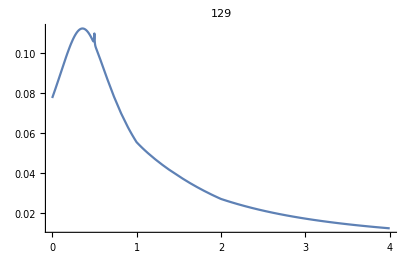

Potential for Nn=229

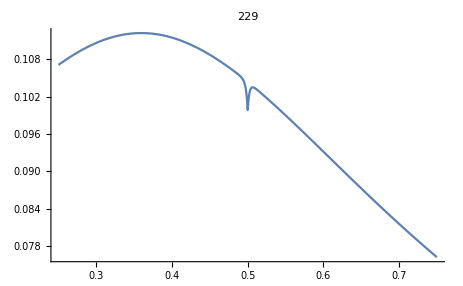
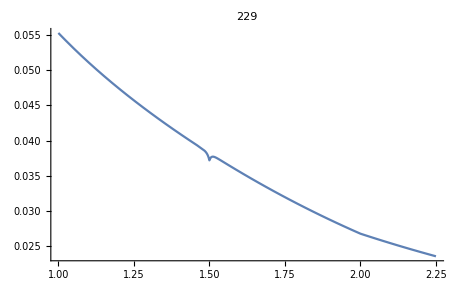
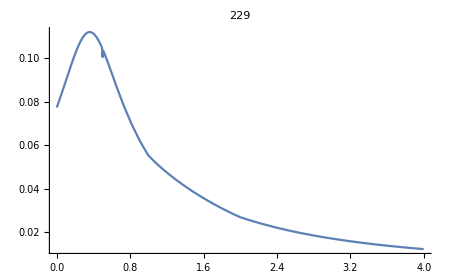

Potential for Nn=329

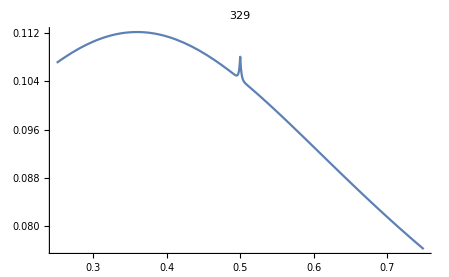
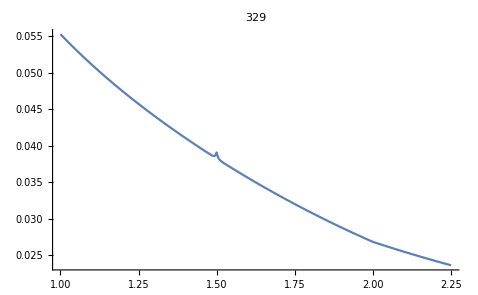
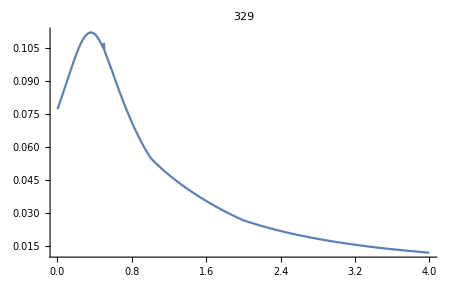

Potential for Nn=451

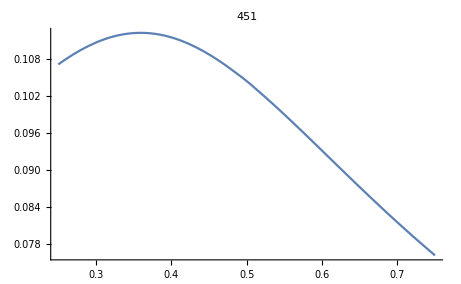
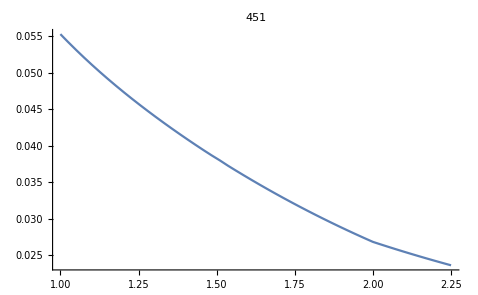
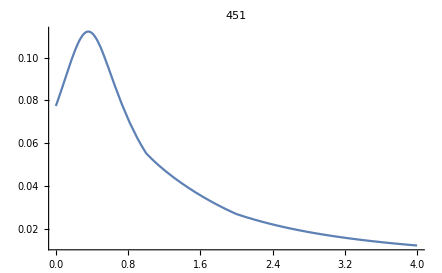

Potential for Nn=452

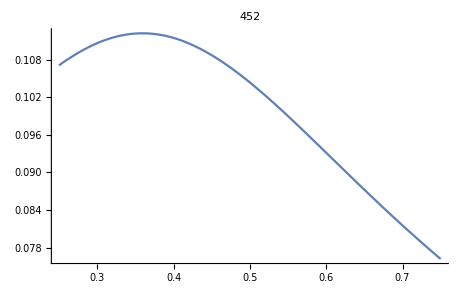
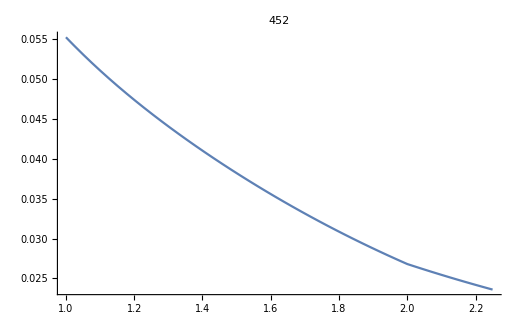
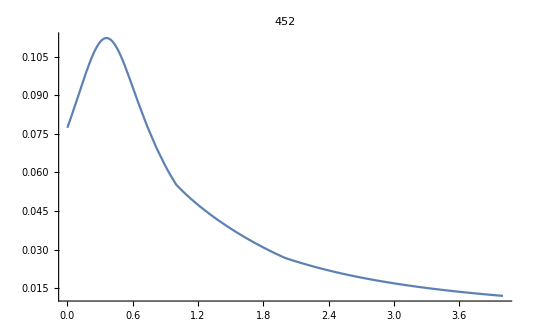

# 8) Polarization charge -Graphics-

Fig .4. q1 was not represented to simplify the figure. Its coordinates are analogous with those for q2.

```mathematica
(*POTENTIALS for the geometry from Fig.4*)
Clear["Global`*"];
ClearAll;
ct=(4*π*ϵ0)^-1;
P[n_,t_]:=LegendreP[n,Cos[t]];
A1[n_]:=Simplify[(ct * q1 *s1^n)/R^(1+2 n)PereA1equiv[n]]; B1[n_]:=Simplify[(ct *q1 *s1^n)/R^(1+2 n)PereB1equiv[n]]; 
C1[n_]:=Simplify[ct *q1 * s1^n PereC1equiv[n]]; D1[n_]:=Simplify[ct* q1 * s1^n PereD1equiv[n]];
PereA1equiv[n_]:=(1/(ϵ1* Dn[n])(1+n)((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)/r0^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (ϵ2-ϵ3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (ϵ3+(ϵ2+ϵ3) n))/Dn[n])^1;
PereD1equiv[n_]:=((ϵ2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
A2[n_]:=ct* PereA2equiv[n,s2]*q2 * s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2 * s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2 * r0^(1+2 n) *s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  *r0^(1+2 n) *s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((ϵ3+(ϵ2+ϵ3) n) +(ϵ2-ϵ3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ2-ϵ3) (1+n)  ((-ϵ1+ϵ2) n r0^(1+2 n)/R^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ1-ϵ2)   (-n (ϵ3+(ϵ2+ϵ3) n) +(-ϵ2+ϵ3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(ϵ1-ϵ2) n +(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/r0^(1+2 n)))/Dn[n])^1;
P[n_,θ_]:=LegendreP[n,Cos[θ]];
PA[n_,m_,θ_]:=LegendreP[n,m,Cos[θ]];
(*eq. 19:*)
PP[n_,θ_,α_,φ_,β_]:=P[n,θ]*P[n,α]+2*∑_(m=1)^n (((n-m)!)/((n+m)!)*PA[n,m,θ]*PA[n,m,α]*Cos[m*(φ-β)]);
ϕ1L[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*PP[n,θ,θ1,φ,φ1];
ϕ12[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*PP[n,θ,θ1,φ,φ1];
ϕ13[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn D1[n]*r^(-n-1)*PP[n,θ,θ1,φ,φ1];
ϕ21[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn A2[n]*r^n*PP[n,θ,θ2,φ,φ2];
ϕ2S[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)*(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*PP[n,θ,θ2,φ,φ2];
ϕ2L[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*PP[n,θ,θ2,φ,φ2];
ϕ23[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn D2[n]*r^(-n-1)*PP[n,θ,θ2,φ,φ2];
```

```mathematica
(*FIELDS for the geometry from Fig.4*)
ϵ1L[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ1L[s1,r,θ,θ1,φ,φ1],r];
ϵ12[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ12[s1,r,θ,θ1,φ,φ1],r];
ϵ13[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ13[s1,r,θ,θ1,φ,φ1],r];

ϵ21[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ21[s2,r,θ,θ2,φ,φ2],r];
ϵ2S[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ2S[s2,r,θ,θ2,φ,φ2],r];
ϵ2L[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ2L[s2,r,θ,θ2,φ,φ2],r];
ϵ23[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ23[s2,r,θ,θ2,φ,φ2],r];
```

```mathematica
(*---------------------*)
(* check with Jackson (4.47), p.157: *)
ϵ0=1;ϵ1=4;ϵ2=8;ϵ3=8;
q1=1;q2=0;
(*---------------------*)

r0=1.; R=2*r0;s1=r0/2;s2=3*r0/2;
ϵ0=1;ϵ1=2;ϵ2=3;ϵ3=4;
q1=1;q2=1;
ϵ0=1;ϵ1=4;ϵ2=8;ϵ3=8;
q1=1;q2=0;
χ1=ϵ1-1;
χ2=ϵ2-1;
χ3=ϵ3-1;
Nn=10;
θ1=Pi-Pi/6;
θ2=Pi-Pi/4;
φ1=0;
φ2=Pi/3;
(*
Expressions for the surface polarization charge density:
*)
σ12[s1_,s2_,θ_,θ1_,θ2_,φ_,φ1_,φ2_]:=-(χ2*ϵ12[s1,r,θ,θ1,φ,φ1]-χ1*ϵ1L[s1,r,θ,θ1,φ,φ1]+χ2*ϵ2S[s2,r,θ,θ2,φ,φ2]-χ1*ϵ21[s2,r,θ,θ2,φ,φ2])/.r->r0;
σ23[s1_,s2_,θ_,θ1_,θ2_,φ_,φ1_,φ2_]:=-(χ3*ϵ13[s1,r,θ,θ1,φ,φ1]-χ2*ϵ12[s1,r,θ,θ1,φ,φ1]+χ3*ϵ23[s2,r,θ,θ2,φ,φ2]-χ2*ϵ2L[s2,r,θ,θ2,φ,φ2])/.r->R;

θ=π/4;
φ=π/4;
Print["σ12[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=",σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2]];
Print["σ23[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=",σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2]];
Clear[θ,φ];
Desig={"a)","b)","c)","d)"};
Q1={1,1,-1,1};
Q2={0,1,1,1};
Phi1={0,0,0,0};
Theta1={0,0,0,0};
Phi2={0,0,0,0};
Theta2={Pi/2,Pi/2,3Pi/4,3Pi/4};
(*We used a For cycle to represent more than one figure at once*)
For[i=1,i<=4,i++,
φ1=Phi1[[i]];
φ2=Phi2[[i]];
θ1=Theta1[[i]];
θ2=Theta2[[i]];
q1=Q1[[i]];
q2=Q2[[i]];
Tσ=Flatten[Table[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2]},{φ,0, 2π},{θ,0,π}],2];
Print["minσ=",minσ=Min[Tσ]];
Print["maxσ=",maxσ=Max[Tσ]];
minσ12=First[NMinimize[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
maxσ12=First[NMaximize[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
minσ23=First[NMinimize[{σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
maxσ23=First[NMaximize[{σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
(*Do not use NelderMead! The other methods give the same results as far as we tested*)
Print[minσ=Min[minσ12,minσ23]];
Print[maxσ=Max[maxσ12,maxσ23]];
(*minσ=Min[Tσ];
maxσ=Max[Tσ];*)
p1=ParametricPlot3D[r0*{Cos[φ]*Sin[θ],Sin[φ]*Sin[θ],Cos[θ]},{φ,0, 2π},{θ,0,π},Mesh->False,ColorFunction->(Function[{x,y,z,φ,θ},ColorData["TemperatureMap"][Rescale[σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],{minσ,maxσ}]]]),
PlotStyle->Directive[(*GrayLevel[0],*)Opacity[0.6]],ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{ColorData["TemperatureMap"],{minσ,maxσ}},ColorFunctionScaling->True,LabelStyle->Directive[20,Bold],LegendLayout->"Row",LegendMarkerSize->300,Ticks->{-0.15,-0.1,-0.05,0,0.05,0.1,0.15}],{0.5,0.025}],Axes->None,Boxed->False,Ticks->None,ViewPoint->{Pi,Pi/2,2},ViewAngle->Pi/12,PlotLabel->Style[Desig[[i]],Bold,40]];
p2=ParametricPlot3D[R*{Cos[φ]*Sin[θ],Sin[φ]*Sin[θ],Cos[θ]},{φ,0,π},{θ,0,π},Mesh->False,ColorFunction->(Function[{x,y,z,φ,θ},ColorData["TemperatureMap"][Rescale[σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],{minσ,maxσ}]]]),
PlotStyle->Directive[(*GrayLevel[0],*)Opacity[0.6]],ColorFunctionScaling->False,Boxed->False,Axes->False];
p3=ListPointPlot3D[{{s1*Sin[θ1]*Cos[φ1],s1*Sin[θ1]*Sin[φ1],s1*Cos[θ1]},{s2*Sin[θ2]*Cos[φ2],s2*Sin[θ2]*Sin[φ2],s2*Cos[θ2]}},PlotStyle->Directive[Black,PointSize[0.03]],Boxed->False,Axes->False];
p4=Graphics3D[{If[θ2≠0,{Dashed,Thick,Line[{{0,0,0},{s2*Sin[θ2]*Cos[φ2],s2*Sin[θ2]*Sin[φ2],s2*Cos[θ2]}}]},],If[θ1≠0,{Dashed,Thick,Line[{{0,0,0},{s1*Sin[θ1]*Cos[φ1],s1*Sin[θ1]*Sin[φ1],s1*Cos[θ1]}}]},],Text[Style["x",32],{2.35,-0.15,0}],Text[Style["y",32],{-0.2,2.4,0}],Text[Style["z",32],{0,0,2.4}],{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{0,2.3,0}}]}},{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{2.3,0,0}}]}},{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{0,0,2.15}}]}}}];
Print[Show[p1,p2,p3,p4,PlotRange->All]]]
```

σ12[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=-0.0049118

σ23[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=0

minσ=-0.047027

maxσ=0

-0.04702701306

0

-Graphics-

minσ=-0.0481311

maxσ=0.00108685

-0.04813112558

0.01706497535

-Graphics-

minσ=-1.82146×10^-17

maxσ=0.0460665

0

0.04606650446

$Aborted